```mathematica
SetDirectory[NotebookDirectory[]];
```

{{a→κ,b→κ/(κ+μ)}}

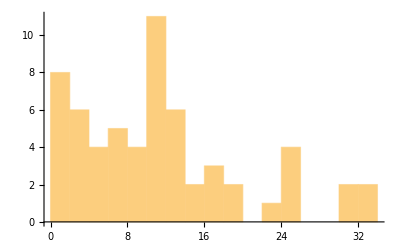

10.9

```mathematica
Clear[μ,κ,a,b]
size = 60;
Solve[{(a (1-b))/b==μ,(a (1-b))/b^2==μ + ((μ^2)/κ)},{a,b}]
μ = 10;
κ = 1.5;
a = κ;
b = κ/(κ+μ);
realData=RandomVariate[NegativeBinomialDistribution[a,b],{size}];
Histogram[realData,20]
xbar = N@Mean@realData
```

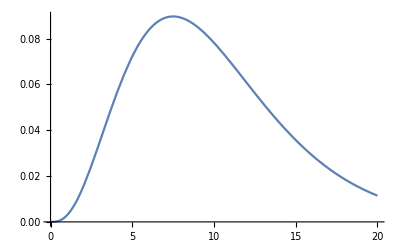

```mathematica
α = 4;
β = 0.4;
Plot[PDF[GammaDistribution[α,1/β],x],{x,0,20}]
```

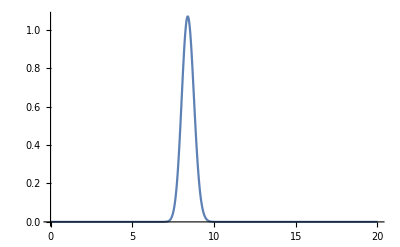

```mathematica
Plot[PDF[GammaDistribution[size*xbar + α,1/(β+size)],x],{x,0,20},PlotRange->Full]
```

```mathematica
Integrate[PDF[GammaDistribution[α,1/β],λ]*Likelihood[PoissonDistribution[λ],realData],{λ,0,∞}]
```

1.758×10^-143

```mathematica
NIntegrate[PDF[GammaDistribution[α,1/β],n]*PDF[BetaDistribution[1,1],p]*Likelihood[NegativeBinomialDistribution[n,p],realData],{p,0,1},{n,0,∞}]
```

2.71296×10^-93

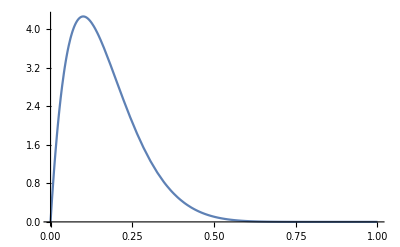

```mathematica
Plot[PDF[BetaDistribution[2,10],p],{p,0,1}]
```